```mathematica
Needs["PlotLegends`"]
expr[x_,y_] := 2*x*y/(x^2-1); (*the function that will be ploted*)
Manipulate[Plot[ArcTan[expr[x,y]], {x,0,2}],{y,0.1,1}] (*playing around with the function*)
```

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

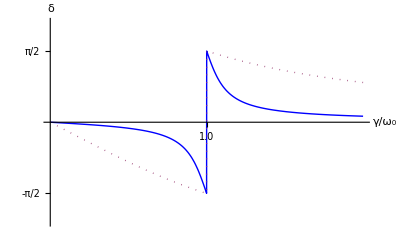

```mathematica
temp1=Table[{0.25*i,""},{i,3}];
temp2 = Table[{1+0.25*i,""},{i,3}];
xTicks = Join[temp1,{{1,"1.0"}}, temp2]; (*x axis ticks in format of { {tick1, tick1 label}, {tick2, tick2 label}, etc... }*)

ticks = { xTicks, 
(*begin y axis ticks*){ {-Pi/2,-Pi/2,{1,0},Directive[Dashed]} (*y tick 1*), {-Pi/4, ""} (*minor unlabeled tick*),
{Pi/2,Pi/2,{1,0},Directive[Dashed]} (*y tick 3*), {Pi/4, ""}}  (*end y ticks*)} (*end ticks*) ;

Plot[{ArcTan[expr[x,0.1]],ArcTan[expr[x,0.9]]}, 
{x,0,2}, 
PlotStyle-> {Blue,{Thick,Dotted}},
AxesLabel-> {(γ/Subscript[ω, 0]),δ},
Ticks->ticks,
PlotRange->{{0,2},{-2.2,2.2}},
AxesStyle->Arrowheads[0.03] (*add arrows to the axes*), 
PlotLegend-> {"λ/ω_0 = 0.1","λ/ω_0 = 0.9"},
LegendPosition->{1.1,-0.4},
LegendShadow-> {0.01,-0.01},
LegendSize->{0.5,0.5}]
```